# Arduino Tests

## Open the Device

Connect your Arduino UNO to the USB port and then check out the following line of code:

```mathematica
arduino=DeviceOpen["Arduino","COM60"]
```

```mathematica
Manipulate[
DeviceWrite[arduino,11->pwm/255],{pwm, 0, 255}
]
```

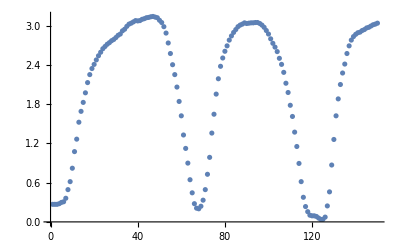

```mathematica
ListPlot[pressure = DeviceReadList[arduino, 150, "A5"]]
```

```mathematica
pF= ListInterpolation[QuantityMagnitude[pressure], {0, 3}]
```

InterpolatingFunction[…]

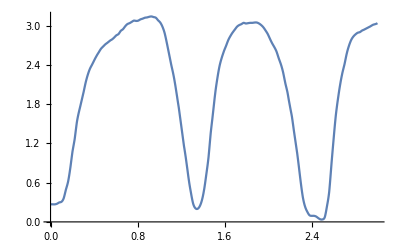

```mathematica
Plot[pF[t], {t, 0, 3}]
```

```mathematica
w = Table[Sin[pF[t]/3 *1000*t*2π], {t, 0, 3, 1/10000}];
```

```mathematica
MinMax[w]
```

{-1.,1.}

```mathematica
ListPlay[w, SampleRate->10000]
```

-Graphics-

```mathematica
DeviceClose[arduino]
```

```mathematica
Cell[BoxData[
 RowBox[{"{", 
  GraphicsBox[
   {RGBColor[1., 0., 0.], Thickness[0.05], Opacity[1.], CapForm["Butt"], JoinForm[{"Miter", 4.}], 
    JoinedCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{145.85500000000002`, 64.42888900000001}, {145.85500000000002`, 28.924889000000007`}, {113.238, 
     0.13988900000003923`}, {73., 0.13988900000003923`}, {32.76200000000001, 0.13988900000003923`}, {0.14100000000000001`, 28.924889000000007`}, {0.14100000000000001`,
      64.42888900000001}, {0.14100000000000001`, 99.93288900000002}, {32.76200000000001, 128.71388900000002`}, {73., 128.71388900000002`}, {113.238, 
     128.71388900000002`}, {145.85500000000002`, 99.93288900000002}, {145.85500000000002`, 64.42888900000001}}},
     CurveClosed->{1}]},
   AspectRatio->Automatic,
   ImageSize->{146., 129.},
   PlotRange->{{0., 145.99774200000002`}, {0., 128.85488900000001`}}], "}"}]], "Input"]
```